# Lab Work 1, variant 7

## Theory for lab work

```mathematica
ΔX=.;i=.;X=.;n=.;W=.;WW=.;
Y[X_]:=X.W;
X'[Y_]:=Y.W';
ΔX:=X'-X;
ΔW':=α Transpose[Y].ΔX;
ΔW:=α Transpose[X].ΔX.Transpose[W'];
Err:=1/2 Sum[Sum[Subscript[ΔX[Subscript[X, j],W,WW], i]^2,{i,1,Length[ΔX[Subscript[X, j],W,WW]]}]//HoldForm,{j,1,n}];
Print[HoldForm[Y[X]//TraditionalForm],"=",Y[X]//TraditionalForm]
Print[HoldForm[X'[Y]//TraditionalForm],"=",X'[Y]//TraditionalForm]
Print[HoldForm[ΔX//TraditionalForm],"=",ΔX//TraditionalForm]
Print[HoldForm[ΔW//TraditionalForm],"=",ΔW//TraditionalForm]
Print[HoldForm[ΔW'//TraditionalForm],"=",ΔW'//TraditionalForm]
Print[HoldForm[Err//TraditionalForm],"=",Err//TraditionalForm]
```

Y(X)=X.W

X'(Y)=Y.W'

ΔX=X'-X

ΔW=α X^ᵀ.(X'-X).W'^ᵀ

ΔW'=α Y^ᵀ.(X'-X)

Err=1/2 ∑_(j=1)^n ∑_(i=1)^Length[ΔX(X_j,W,WW)] (ΔX(X_j,W,WW))_i^2

## Function's definition

### Functions for data preparing

```mathematica
openSaveDialogFilter = {"",{"Image file"->{"*.bmp"}}};
GetInputData = (Flatten[Flatten[#]&/@#&/@Partition[Import[#1, "Data"],{#2,#3}],1])&;
ConvertColours = (( 2*#/255-1)&/@#&/@#)&;
BackvertColours = (( 255*(#+1)/2)&/@#&/@#)&;
GetOutputData =(Block[{nn,widthCount},nn=#2;widthCount=#3/nn;Join@@#&/@Flatten[(Transpose[#]&/@ Partition[(Partition[#,nn])&/@ ((Partition[#,3])&/@ #1),widthCount]),1]])&;
CorrectColours = (If[AtomQ[#],r=Round[#];Max[0,Min[255, r]],CorrectColours[#]&/@#])&;
NormalizeW = Compile[{{x,_Real,2}}, Transpose[Normalize[#]&/@Transpose[x]]];
RestartTraining=Function[{nn,mm,pp},W= NormalizeW[ RandomReal[{-1,1},{nn*mm*3,pp}]];
W' =NormalizeW[RandomReal[{-1,1},{pp,nn*mm*3}]];trainingIteration=0;];
```

```mathematica
PrintImages=(Block[{outputData},outputData = CorrectColours[GetOutputData[BackvertColours[X'],n,width]];
SetDirectory[$TemporaryPrefix];
Export["temp.bmp",outputData,"Data"];
newImage=Import["temp.bmp"];
ResetDirectory[];
])&;
```

```mathematica
ShowButtons=({{Button["Restart",If[controlFlag==0,controlFlag++;RestartTraining[n,m,p]
TrainingNetwork[X,W,W'],0],Method->"Queued"],Button["Stop",controlFlag=0,Method->"Preemptive"],Button["Continue",If[controlFlag==0,controlFlag++;TrainingNetwork[X,W,W'],0],Method->"Queued"]}}//TableForm)&;
```

### Functions from theory

```mathematica
FunctionE =Compile[{{x, _Real, 2}},Plus @@( (#^2)&/@ Flatten[x])];
```

```mathematica
TrainingStep = Compile[{{x,_Real, 2},{w,_Real, 2},{wr,_Real, 2},{_α,_Real}},Block[{Y,ΔX},Y =x.w ;restoredX = Y.wr;ΔX = restoredX-x;forPackW= NormalizeW[w-_α*Transpose[x].ΔX.Transpose[wr]];forUnpackW=NormalizeW[wr - _α*Transpose[Y].ΔX];ΔX]];
```

```mathematica
TrainingNetwork=Compile[{{x,_Real, 2},{w,_Real, 2},{wr,_Real, 2}},Block[{forPackW,forUnpackW,deltaX,restoredX},forPackW=w;forUnpackW=wr;restoredX=x;deltaX=TrainingStep[x,forPackW,forUnpackW,α];trainingIteration++;While[(ce=FunctionE[deltaX])> err && controlFlag!=0, deltaX=TrainingStep[x,forPackW,forUnpackW,α];trainingIteration++];W=forPackW;W'=forUnpackW;X'=restoredX;];];
```

## Input parameters

```mathematica
imageName = SystemDialogInput["FileOpen",openSaveDialogFilter];
{width,height} =Import[imageName, "ImageSize"];
Print["Width:",width," Height:",height]
n=2;
m=2;
α = 0.007;
err = 10;
p = 6;
Z = (p*((height*width)/(n*m)+n*m*3))/(3*width*height);
originalImage=Import[imageName];
Print["Packing coefficient: ",Z,"=",Z//N]
```

Width:8 Height:8

Packing coefficient: 7/8=0.875

## Preparing data

```mathematica
X = ConvertColours[GetInputData[imageName,n,m]]//N;
RestartTraining[n,m,p];
trainingIteration=0;
controlFlag=0;
```

## Training

```mathematica
Print["Number of iterations: ",Dynamic[trainingIteration]," MSE: ",Dynamic[ce]]
ShowButtons[]
Button["Print images",PrintImages[],Method->"Queued"]
Dynamic[GraphicsRow[{originalImage,newImage},ImageSize->{500,500}]]
```

Number of iterations:  MSE:

Restart | Stop | Continue

Print images

## Lab work report

```mathematica
(*iteration from Z*)
```

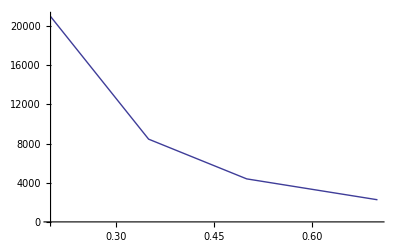

```mathematica
ListLinePlot[{{0.2, 20989},{0.35, 8453},{0.5,4395},{0.7,2261}}]
```

```mathematica
(*iteration from image*)
```

```mathematica
(*For images t4.bmp, t2.bmp*)
(*(* Изображение t2 хорошо сегментированно,
 что позволяет обучаться за меньшее число шагов
 по сравнению с другим изображением,совподающего размера *)*)
```

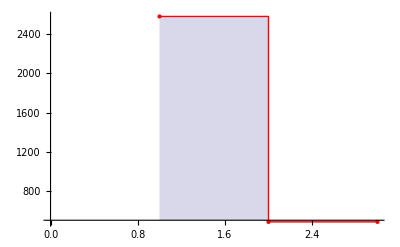

```mathematica
ListLinePlot[{2582, 483,483},PlotStyle->{Red},Mesh -> Full,Filling-> Axis,InterpolationOrder->0]
```

```mathematica
(*iteration from e*)
```

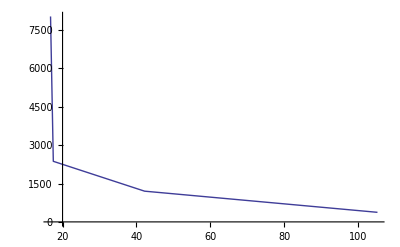

```mathematica
ListLinePlot[Sort[{{105.2,374},{42.2, 1201},{17.5,2368},{16.75,8030}}]]
```

```mathematica
(*iteration from α*)
```

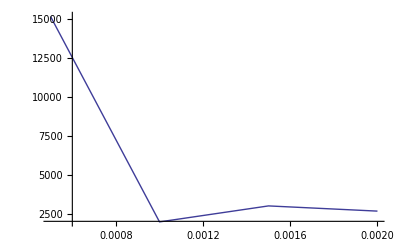

```mathematica
ListLinePlot[Sort[{{0.0015, 2989},{0.001,1964},{0.0005,15135},{0.002,2655}}]]
```